## RMS - test fit

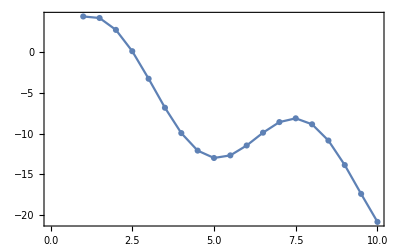

```mathematica
fct[i1_,i2_,i3_,θ_,x_]:=i1*Sin[x]-i2 *x+i3+θ*x;
params={5.2,1.9,2.0,-0.1};
xvalues=Table[i,{i,1,10,0.5}];
fvalues[x_,params_]:=Table[{x[[i]],fct[params[[1]],params[[2]],params[[3]],params[[4]],x[[i]]]},{i,1,Length[x]}];
plot[xvalues_,params_]:=ListPlot[fvalues[xvalues,params],Frame->True,Axes->False,Joined->True,PlotMarkers->Automatic];
Show[plot[xvalues,params]]
```

```mathematica
fvalues[xvalues,params]
```

{{1.,4.37565},{1.5,4.18697},{2.,2.72835},{2.5,0.112055},{3.,-3.26618},{3.5,-6.82407},{4.,-9.93537},{4.5,-12.0832},{5.,-12.9864},{5.5,-12.6688},{6.,-11.453},{6.5,-9.88138},{7.,-8.58367},{7.5,-8.1224},{8.,-8.85534},{8.5,-10.8479},{9.,-13.857},{9.5,-17.3908},{10.,-20.8289}}

```mathematica
FindFit[fvalues[xvalues,params],fct[a,b,c,d,x],{a,b,c,d},x]
```

{a→5.2,b→1.,c→2.,d→-1.}